## A Workbook that builds the simulators found in Section 9.5 and 9.6 in Systems Biology: Dynamic states of networks Niko Sonnenschein and Bernhard Palsson Dec 2012

### Initialize Toolbox

```mathematica
<<Toolbox`Style`
<<Toolbox`
```

## Feedback Inhibition of Pathways

The local regulation of a reaction by its reactants or products has just been analyzed. We now turn our attention to situations where a reaction is regulated by a compound that is far away in the network and how to build simulation models of such regulatory phenomena. We can use simulation and case studies to determine the effectiveness of the regulatory action. We will now use elementary reactions to describe the regulatory mechanism. We now turn our attention to situations where a reaction is regulated by a compound that is far away in the network and how to build simulation models of such regulatory phenomena. We can use simulation and case studies to determine the effectiveness of the regulatory action. We will now use elementary reactions to describe the regulatory mechanism.

In a biosynthetic pathway, the first reaction is often inhibited by the end product of the pathway, see schema. A metabolic intermediate, x_1, is being formed, and degraded as

→^b_1 x_1→^k_0

Then, if an enzyme, x_6, is expressed, x_1 can be converted to x_2

x_1+x_6→^k_1 x_2

that is followed by a series of reactions

x_2→^k_2 x_6+x_3→^k_3 x_4→^k_4 x_5→^k_5

to form x_5, that is an end product of the pathway. The end product does feedback inhibit the enzyme, x_7, by binding to it and converting it into an inactive form:

| k_6 | 
x_6+x_5 | ⇌ | x_7
 | k_-6 |

This system represents a simple negative feedback loop. And is illustrated by

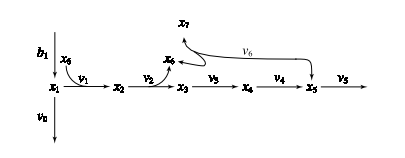

### Define model

The model is defined by simply writing down the system of reactions involved, in addition to specifying the numerical values for the rate constants.

```mathematica
model=constructModel[
{(∅->x1)^b1,(x1->∅)^0,Overscript[x1+x6->x2, 1],Overscript[x2->x3+x6, 2],Overscript[x3->x4, 3],Overscript[x4->x5, 4],(x5->∅)^5,Overscript[x5+x6⇌x7, 6]},Parameters->{Subscript[k, b1]^⟶->0.1 Hour^-1,Subscript[k, 0]^⟶->0.5 Hour^-1,Subscript[k, 1]^⟶->1000. Liter Hour^-1 Mole^-1,Subscript[k, 2]^⟶->1. Hour^-1,Subscript[k, 3]^⟶->1. Hour^-1,Subscript[k, 4]^⟶->1. Hour^-1,Subscript[k, 5]^⟶->1. Hour^-1,Subscript[k, 6]^⟵->1. Hour^-1,Subscript[k, 6]^⟶->10 Liter Hour^-1 Millimole^-1,x1^Xt->1/1000 Mole Liter^-1},UnitChecking->True];
```

### Specify initial conditions

The initial conditions here are obtained from solving the steady state equations for these numerical values of the rate constants. The differential equations that describe this feedback loop and that have to be numerically simulated are

```mathematica
model["ODE"]//TableForm
```

x1'[t]==x1^Xt k_b1^⟶-k_0^⟶ x1[t]-k_1^⟶ x1[t] x6[t]
x2'[t]==-k_2^⟶ x2[t]+k_1^⟶ x1[t] x6[t]
x3'[t]==k_2^⟶ x2[t]-k_3^⟶ x3[t]
x4'[t]==k_3^⟶ x3[t]-k_4^⟶ x4[t]
x5'[t]==k_4^⟶ x4[t]-k_5^⟶ x5[t]-k_6^⟶ x5[t] x6[t]+k_6^⟵ x7[t]
x6'[t]==k_2^⟶ x2[t]-k_1^⟶ x1[t] x6[t]-k_6^⟶ x5[t] x6[t]+k_6^⟵ x7[t]
x7'[t]==k_6^⟶ x5[t] x6[t]-k_6^⟵ x7[t]

The steady-state equations that have to be solved are

```mathematica
TableForm[ssEq=stripTime[model["ODE"]]/._metabolite'[t]:>0]
```

0==-x1 k_0^⟶-x1 x6 k_1^⟶+x1^Xt k_b1^⟶
0==x1 x6 k_1^⟶-x2 k_2^⟶
0==x2 k_2^⟶-x3 k_3^⟶
0==x3 k_3^⟶-x4 k_4^⟶
0==x4 k_4^⟶-x5 k_5^⟶+x7 k_6^⟵-x5 x6 k_6^⟶
0==-x1 x6 k_1^⟶+x2 k_2^⟶+x7 k_6^⟵-x5 x6 k_6^⟶
0==-x7 k_6^⟵+x5 x6 k_6^⟶

One conserved moiety exists in the system:

```mathematica
NullSpace[modelᵀ].model["Species"]
```

{x2+x6+x7}

Solving the steady-state equations and conservation relation for the species variables yields two solutions

```mathematica
{x1,x2,x3,x4,x5,x6,x7}//Length
```

7

```mathematica
ssEq//Length
```

7

```mathematica
ssSol=Solve[Join[ssEq,{x2+x6+x7==p["moiety"]}],{x1,x2,x3,x4,x5,x6,x7}];
Length[ssSol]
SlideView[ssSol[[1]]]
SlideView[ssSol[[2]]]
```

2

Substituting the parameter values and moiety reveals that only the second solution contains exclusively positive concentrations.

```mathematica
ssConc=ssSol/.model["Parameters"]/.p["moiety"]->1Millimole Liter^-1/.n_Real?(#<0&):>Style[n,Red];
SlideView[TableForm/@ssConc]
```

Now we can include the calculated steady-state concentrations as initial conditions in the model.

```mathematica
updateInitialConditions[model,ssConc[[2]]]
```

```mathematica
model["InitialConditions"]
model["Parameters"]
```

{x1→0.090098 Millimole Liter^-1,x2→0.054951 Millimole Liter^-1,x3→0.054951 Millimole Liter^-1,x4→0.054951 Millimole Liter^-1,x5→0.054951 Millimole Liter^-1,x6→0.609902 Millimole Liter^-1,x7→0.335147 Millimole Liter^-1}

{k_b1^⟶→0.1 Hour^-1,k_0^⟶→0.5 Hour^-1,k_1^⟶→1. Liter Hour^-1 Millimole^-1,k_2^⟶→1. Hour^-1,k_3^⟶→1. Hour^-1,k_4^⟶→1. Hour^-1,k_5^⟶→1. Hour^-1,k_6^⟵→1. Hour^-1,k_6^⟶→10 Liter Hour^-1 Millimole^-1,x1^Xt→Millimole Liter^-1}

### Simulate model

We now simulate the model response. Nothing happens as the system starts at steady state and there is nothing perturbing it away from the steady state. So it just stays there.

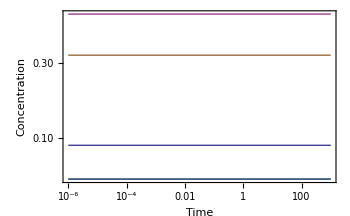

```mathematica
plotSimulation[simulate[model,{t,0,1000}][[1]],FrameLabel->{"Time","Concentration"}]
```

### Visualize model

The MASStoolbox can be used to visualize the network and the reaction schema.  This layout looks different from the layout given above, but it is is the same network.  This layout is computer generated, the above is man made.  The equations are the same, but the visual representation differs.  Thus the model is unique, whereas the graphical visualization is not.

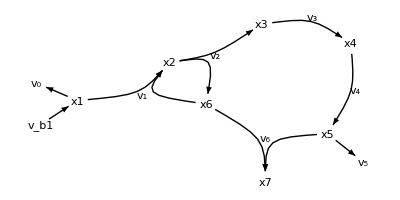

```mathematica
Toolbox`Private`showNetwork[model]
```

### Null spaces and their content

We begin our analysis by looking at the contents of the two null spaces.  These are topological quantities that are condition independent.  That is these properties are always the same regardless of the numberical values of the parameters and the steady state.

The right null space has two pathways, one goes from the primary input (b1) and out of the primary pathway and one goes from the primary input (b1) and out of the biosynthetic pathway.

```mathematica
TableForm[NullSpace@model,TableHeadings->{None,model["Fluxes"]}] 
TableForm[NullSpace[model].model["Fluxes"]]
```

v_b1 | v_0 | v_1 | v_2 | v_3 | v_4 | v_5 | v_6
1 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0

v_1+v_2+v_3+v_4+v_5+v_b1
v_0+v_b1

```mathematica
highlight=List@@@(NullSpace[model].model["Fluxes"])/.flux_v:>(flux->Style[flux,Large,Background->Green])
```

{{v_1→v_1,v_2→v_2,v_3→v_3,v_4→v_4,v_5→v_5,v_b1→v_b1},{v_0→v_0,v_b1→v_b1}}

Visualize the two pathway vectors on the network map

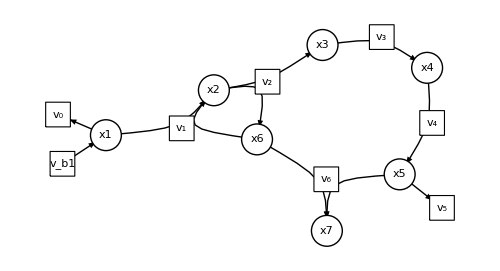
{-Graphics-,-Graphics-}

```mathematica
Show[showNetwork[model]/.#,ImageSize->500]&/@highlight
```

The left null space has one pool: the conservation of the enzyme that is found in the active form (x6), in the intermediary complex (x2) or in the inhibited form (x7) when it is bound to the inhibitor (x5)

```mathematica
TableForm[NullSpace[modelᵀ],TableHeadings->{None,model["Species"]}]
TableForm[NullSpace[modelᵀ].model["Species"]]
```

x1 | x2 | x3 | x4 | x5 | x6 | x7
0 | 1 | 0 | 0 | 0 | 1 | 1

x2+x6+x7

### Steady states

We now evaluate the steady state for the given numerical values of the kinetic parameters. This is how we obtained the steady state values for the concentrations that were used above in the problem definition. We show two different methods to find the steady state. Solve the algebraic equations when the LHS is equated to zero, and to simulate the system to very long times, where it reached a steady state irregardless of what you chose as the initial conditions (note though that the initial conditions for x2, x6, x7 will set that pool size)

```mathematica
sample=Table[
sol=simulate[model,{t,0,1*^8},InitialConditions->updateRules[#->RandomReal[]Millimole Liter^-1&/@model["Species"],{x6->0.3 Millimole Liter^-1,x7->0.5 Millimole Liter^-1,x2->0.2 Millimole Liter^-1}]][[1]],{10}];
```

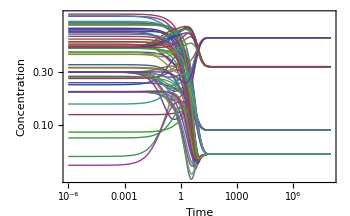

```mathematica
plotSimulation[Flatten@sample,FrameLabel->{"Time","Concentration"}]
```

We now evaluate the steady state for the given numerical values using the Newton method for finding roots numerically

```mathematica
{ssConcNewton,ssFluxesNewton}=findSteadyState[model];
ssConcNewton
```

{x1→0.090098 Millimole Liter^-1,x2→0.054951 Millimole Liter^-1,x3→0.054951 Millimole Liter^-1,x4→0.054951 Millimole Liter^-1,x5→0.054951 Millimole Liter^-1,x6→0.609902 Millimole Liter^-1,x7→0.335147 Millimole Liter^-1}

Simulate from the steady state solution found to show that the system is steady

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 8.42513×10^12.

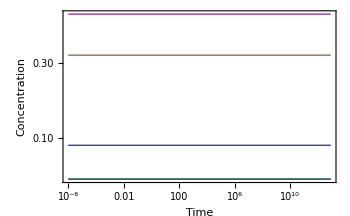

```mathematica
plotSimulation[simulate[model,InitialConditions->ssConcNewton][[1]],FrameLabel->{"Time","Concentration"}]
```

Simulates system from a single initial condition

```mathematica
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate];
```

```mathematica
ssConc
```

{x1→0.0900993 Millimole Liter^-1,x2→0.0549503 Millimole Liter^-1,x3→0.0549503 Millimole Liter^-1,x4→0.0549503 Millimole Liter^-1,x5→0.0549503 Millimole Liter^-1,x6→0.609886 Millimole Liter^-1,x7→0.335134 Millimole Liter^-1}

Simulates system for a 10x increase in b1 at t=0

```mathematica
{ssConcAfterPerturb,ssFluxesAfterPerturb}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> 10*(0.1/Hour)}]
```

{{x1→1.44575 Millimole Liter^-1,x2→0.277124 Millimole Liter^-1,x3→0.277124 Millimole Liter^-1,x4→0.277124 Millimole Liter^-1,x5→0.277124 Millimole Liter^-1,x6→0.191681 Millimole Liter^-1,x7→0.531195 Millimole Liter^-1},{v_b1→1. Millimole Hour^-1 Liter^-1,v_0→0.722876 Millimole Hour^-1 Liter^-1,v_1→0.277124 Millimole Hour^-1 Liter^-1,v_2→0.277124 Millimole Hour^-1 Liter^-1,v_3→0.277124 Millimole Hour^-1 Liter^-1,v_4→0.277124 Millimole Hour^-1 Liter^-1,v_5→0.277124 Millimole Hour^-1 Liter^-1,v_6→0. Millimole Hour^-1 Liter^-1}}

We can study the steady state solutions by breaking them down into a linear combination of the two pathway vectors in the null space.  These two vectors span the null space and can be used to represent any given valid steady state solution

```mathematica
ss1=stripUnits[ssFluxes[[All,2]]]
ss2=stripUnits[ssFluxesAfterPerturb[[All,2]]]
```

{0.1,0.0450497,0.0549503,0.0549503,0.0549503,0.0549503,0.0549503,0.}

{1.,0.722876,0.277124,0.277124,0.277124,0.277124,0.277124,0.}

```mathematica
null=NullSpace[model]ᵀ;
```

```mathematica
ss1Loadings=PseudoInverse[null].ss1
ss2Loadings=PseudoInverse[null].ss2
```

{0.0549503,0.0450497}

{0.277124,0.722876}

The loadings should add up to b1: a numerical QC/QA

```mathematica
sumss1= Total[ss1Loadings]
sumss2=Total[ss2Loadings]
```

0.1

1.

We can ratio the loadings to see how the relative ‘load-bearing’ of the pathways is in the steady state.  The first pathway (the primary patway) goes from a 55
% of b1 to 28% of b1 after the perturbation

```mathematica
ss1Loadings[[1]]/sumss1
ss2Loadings[[1]]/sumss2
```

0.549503

0.277124

Another way to measure the relative loading is simply to ratio the loadings for the two pathways

```mathematica
Divide@@ss1Loadings
Divide@@ss2Loadings
```

1.21977

0.383363

The Manipulate function in Mathematica allows us to vary a parameter using a slider to see how the solution changes. This allows one to quickly see how the parameters affect the steady state solution.

```mathematica
Module[{concSol,fluxSol,ssConc,ssFluxes},
Manipulate[
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
GraphicsRow[{
BarChart[ssConc[[All,2]],PlotRange->{All,{-0.2,1.5}},ChartLabels->Placed[ssConc[[All,1]],Axis],PlotLabel->"Steady-state concentrations"],
BarChart[ssFluxes[[All,2]],PlotRange->{All,{-0.2,1.4}},ChartLabels->Placed[ssFluxes[[All,1]],Axis],PlotLabel->"Steady-state fluxes"]
},ImageSize->600]
,{{k0,1},0.5,10.}
]
]
AutoCollapse[]
```

An equivalent way to see the parametric sensitivity is to compute the steady state solution as a function of a parameter and plot it.

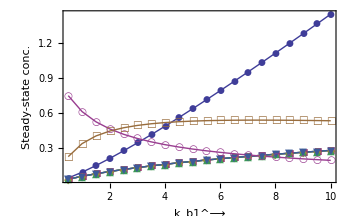

```mathematica
ListPlot[Transpose@Table[
{ssConc,ssFluxes}=findSteadyState[model,"Strategy"->simulate,Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
Thread[{k0,stripUnits@ssConc[[All,2]]}]
,{k0,0.5,10.,.5}
],Joined->True,PlotMarkers->Automatic,Epilog->insetLegend[model["Species"]],FrameLabel->{Subscript[k, b1]^⟶,"Steady-state conc."}]
```

This completes our study of the steady state properties and we can now look at the dynamic states.

### Dynamics states

We will now perform dynamic simulations: first we demonstrate that simulating with the steady states as the initial conditions, nothing happens. Second, we show how the concentration variable scan be called out at particular time points. Third, we simulate the response to a 10-fold change in the input flux b1. Fourth, we demonstrate the use of the function Manipulate[] to manually trace out the time trajectories

#### Initial steady-state

We now demonstrate that simulating with the steady states as the initial conditions, nothing happens

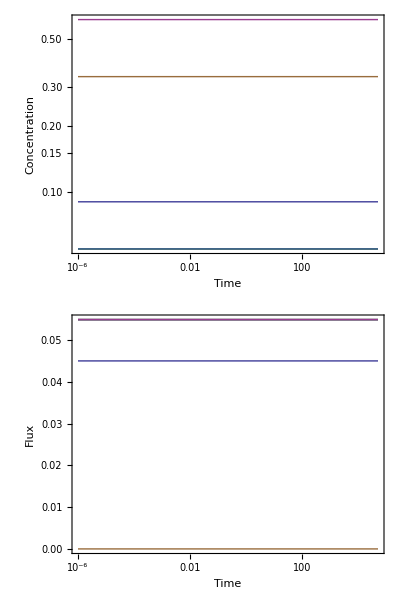

```mathematica
{concSol,fluxSol}=simulate[model,{t,0,50000}];
Column[{plotSimulation[concSol,FrameLabel->{"Time","Concentration"}],plotSimulation[fluxSol,PlotFunction->LogLinearPlot,FrameLabel->{"Time","Flux"}]}]
concSol/.t->50000;
```

We now demonstrate how one calls out the values of the concentraiton at particular times (t=1 and t=3), either the entire solution or a particular concentration

```mathematica
concSol/.t->1
concSol/.t->3
FilterRules[concSol,{x1}]/.t->1
```

{x1→0.090098 Millimole Liter^-1,x2→0.054951 Millimole Liter^-1,x3→0.054951 Millimole Liter^-1,x4→0.054951 Millimole Liter^-1,x5→0.054951 Millimole Liter^-1,x6→0.609902 Millimole Liter^-1,x7→0.335147 Millimole Liter^-1}

{x1→0.090098 Millimole Liter^-1,x2→0.054951 Millimole Liter^-1,x3→0.054951 Millimole Liter^-1,x4→0.054951 Millimole Liter^-1,x5→0.054951 Millimole Liter^-1,x6→0.609902 Millimole Liter^-1,x7→0.335147 Millimole Liter^-1}

{x1→0.090098 Millimole Liter^-1}

Simulate the response to a step change in the input b1 by 10-fold as done in chapter 8 in the book

```mathematica
(*Put your code here*)
(*{concSolPerturbed,fluxSolPerturbed}= ...*)
```

#### We can examine feactiores of the solution using Manipulate[]. The x2^c+x6^c+x7^c pool is constant while x2^c is not over time

```mathematica
TraditionalForm@Manipulate[Evaluate[x2+x6+x7/.concSolPerturbed],{t,0,4}]
TraditionalForm@Manipulate[Evaluate[x2/.concSolPerturbed],{t,0,4}]
```

#### Use Manipulate to observe the dynamics under varying input perturbations

It is always a good idea to localize variables inside Manipulate (see how Module was used for that purpose). Also k1 was not used in the previous code (compare to your original notebook). Keep in mind that parameters that are provided to simulate via the “Parameters” option will overwrite or extend the parameters already provided in the model.

```mathematica
<<Toolbox`
```

```mathematica
{concSol,fluxSol}=simulate[model,{t,0,100},Parameters->{Subscript[k, b1]^⟶ -> 3*(0.1/Hour)}]
```

{x1[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x2[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x3[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x4[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x5[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x6[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x7[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t]}

{x1^Xt k_b1^⟶,k_0^⟶ x1[t],k_1^⟶ x1[t] x6[t],k_2^⟶ x2[t],k_3^⟶ x3[t],k_4^⟶ x4[t],k_5^⟶ x5[t],k_6^⟶ x5[t] x6[t]-k_6^⟵ x7[t]}

{{x1→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x2→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x3→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x4→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x5→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x6→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],x7→(Millimole Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t]},{v_b1→0.3 Millimole Hour^-1 Liter^-1,v_0→(0.5 Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],v_1→(1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t] InterpolatingFunction[{{0.,100.}},<>][t],v_2→(1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],v_3→(1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],v_4→(1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],v_5→(1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t],v_6→(-1. Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t]+(10 Millimole Hour^-1 Liter^-1) InterpolatingFunction[{{0.,100.}},<>][t] InterpolatingFunction[{{0.,100.}},<>][t]}}

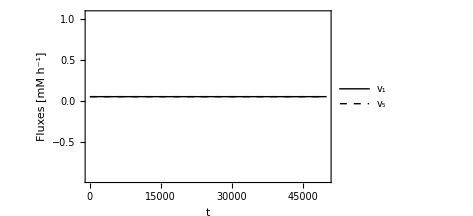

```mathematica
plotSimulation[FilterRules[fluxSol,{v["1"],v["5"]}],FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot,PlotStyle->{Black,Directive[Black,Dashed]},Legend->True]
```

```mathematica
Module[{concSol,fluxSol},
Manipulate[
{concSol,fluxSol}=simulate[model,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
GraphicsGrid[{
{plotSimulation[concSol,FrameLabel->{"t","Concentration [mM]"},PlotFunction->Plot],
plotSimulation[fluxSol,FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot]},
{plotSimulation[FilterRules[fluxSol,{v["1"],v["5"]}],FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot,PlotStyle->{Black,Directive[Black,Dashed]}],Show[plotPhasePortrait[FilterRules[fluxSol,{v["1"],v["5"]}],ColorFunction->None,PlotRange->{{0,1.2},{0,1.2}},Mesh->{{.1,1,10,100}},MeshStyle->Directive[PointSize[.03],Red]],Graphics[{Dashed,Line[{{-1,-1},{2.5,2.5}}]}]]}
},ImageSize->600],{{k0,10,Subscript[k, b1]^⟶},0.5,100.},{{tfinal,40},.1,1000}
]
]
AutoCollapse[]
```

{x1[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x2[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x3[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x4[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x5[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x6[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t],x7[t]→(Millimole Liter^-1) InterpolatingFunction[{{0.,40.}},<>][t]}

### Post-process the solution to set up more insightful plots

```mathematica
poolsOfInterest={"x2+x6"->x2+x6,"x7"->x7}/.concSolPerturbed;

plotPhasePortrait[poolsOfInterest,Mesh->{{0,.1,1,10,100}},MeshStyle->Directive[PointSize[Medium],Red]]
plotSimulation[poolsOfInterest,Legend->True]
```

ReplaceAll::reps: {concSolPerturbed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Toolbox::badargs: There is no definition for 'plotPhasePortrait' applicable to {.

$Aborted

Toolbox::badargs: There is no definition for 'plotSimulation' applicable to {.

$Aborted

## Increasing network complexity

### Regulation of protein synthesis

Define synthesis and degradation reactions for x6 and add them to the model (resulting in a new model). Define a Hill type inhibition rate for the synthesis reaction (no need to define a custom rate equation for the degradation reaction). The final product (x5) acts hereby as the inhibitor. A parameter set is chosen that preserves the steady initial state of the initial model.

```mathematica
synthAndDegradation=str2mass/@{"7: 0 <=> x6","8: x6 -> 0"};
modelWithProtSynth=addReactions[model,synthAndDegradation];
updateCustomRateLaws[modelWithProtSynth,{"7"->Subscript[k, 7]^⟶/(1+Underscript[K, 7] x5[t])}]
updateParameters[modelWithProtSynth,{Subscript[k, 7]^⟶->0.7 Hour^-1,Underscript[K, 7]->178,Subscript[k, 8]^⟶->0.1 Hour^-1}]
```

Visualize the difference between the initial and the extended model

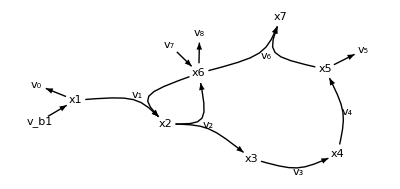

```mathematica
Toolbox`Private`showNetwork[modelWithProtSynth]/.{pat:v["7"]:>Style[pat,Background->Red,Larger],pat:v["8"]->Style[pat,Background->Red,Larger]}
```

Check the model for correctness

```mathematica
TableForm[Thread[{modelWithProtSynth["Reactions"],modelWithProtSynth["Rates"]}]]
```

(∅→x1)^b1 | x1^Xt k_b1^⟶
(x1→∅)^0 | k_0^⟶ x1[t]
(x1+x6→x2)^1 | k_1^⟶ x1[t] x6[t]
(x2→x3+x6)^2 | k_2^⟶ x2[t]
(x3→x4)^3 | k_3^⟶ x3[t]
(x4→x5)^4 | k_4^⟶ x4[t]
(x5→∅)^5 | k_5^⟶ x5[t]
(x5+x6⇌x7)^6 | k_6^⟶ x5[t] x6[t]-k_6^⟵ x7[t]
(∅⇌x6)^7 | k_7^⟶/(1+K_7 x5[t])
(x6→∅)^8 | k_8^⟶ x6[t]

Compare the dynamic behavior of the initial and the extended model

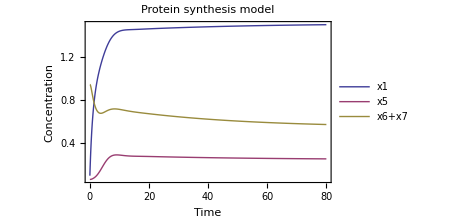
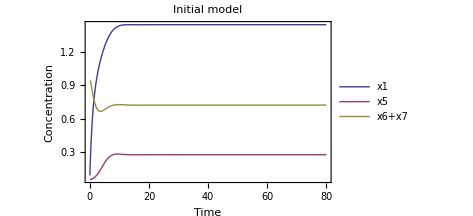

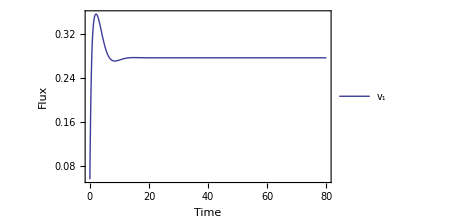
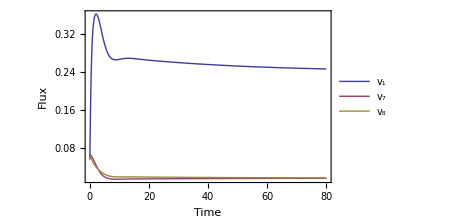

```mathematica
{concSol,fluxSol}=simulate[model,{t,0,80},Parameters->{Subscript[k, b1]^⟶ -> 10*(0.1/Hour)}];
{concSol2,fluxSol2}=simulate[modelWithProtSynth,{t,0,80},Parameters->{Subscript[k, b1]^⟶ -> 10*(0.1/Hour)}];
Row[{plotSimulation[Join[FilterRules[concSol2,{m["x5"],m["x1"]}],{"x6+x7"->m["x6"]+m["x7"]/.concSol2}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time","Concentration"},PlotLabel->"Protein synthesis model"],plotSimulation[Join[FilterRules[concSol,{m["x5"],m["x1"]}],{"x6+x7"->m["x6"]+m["x7"]/.concSol}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time","Concentration"},PlotLabel->"Initial model"]}]
Row[{plotSimulation[FilterRules[fluxSol,{v["1"],v["7"],v["8"]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time","Flux"}],
plotSimulation[FilterRules[fluxSol2,{v["1"],v["7"],v["8"]}],PlotFunction->Plot,Legend->True,FrameLabel->{"Time","Flux"}]}]
AutoCollapse[]
```

Compare the dynamic behavior of the initial and the extended model in phase space

```mathematica
SlideView[Table[plotPhasePortrait[{concSol[[i]],concSol2[[i]]},Mesh->{{0.001,0.01,0.1,1.,10.}},MeshStyle->Directive[Red,PointSize[0.03]]],{i,1,Length[concSol]}]]
```

### Tight regulation of enzyme activity

Allosteric regulation of enzyme activity 
-Graphics-

Define a set of binding reactions for the dimer and tetramer system.

```mathematica
additionalBindingReactions={Overscript[x5+x7⇌x8, 9],Overscript[x5+x8⇌x9, 10],Overscript[x5+x9⇌x10, 11]};
```

#### Dimer

Add the first additional binding reaction and adjust the corresponding rate equations for the effective concentrations of the multiple binding sites.

```mathematica
modelDimer=addReactions[model,{Overscript[x5+x7⇌x8, 9]}];
updateCustomRateLaws[modelDimer,{"6"->2 Subscript[k, 6]^⟶ x5[t] x6[t]-Subscript[k, 6]^⟵ x7[t],"9"->Subscript[k, 6]^⟶ x5[t] x7[t]-2 Subscript[k, 6]^⟵ x8[t]}]
```

Compare the network maps of the initial and the dimer model

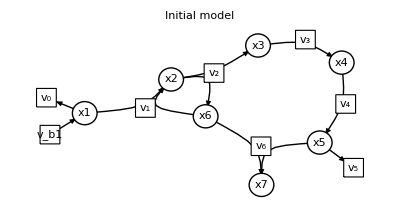

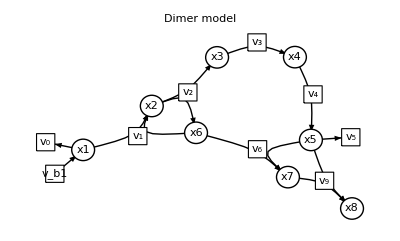

```mathematica
Show[showNetwork[model],PlotLabel->"Initial model"]
Show[showNetwork[modelDimer]/.{Subscript[v, 9]->Style[Subscript[v, 9],Background->Green,Larger],m["x8"]->Style[m["x8"],Background->Green,Larger]},PlotLabel->"Dimer model"]
```

The steady-state equations that have to be solved are

```mathematica
TableForm[ssEq=modelDimer["ODE"]/.Derivative[1][_metabolite][t]:>0/.elem_[t]:>elem]
```

0==-x1 k_0^⟶-x1 x6 k_1^⟶+x1^Xt k_b1^⟶
0==x1 x6 k_1^⟶-x2 k_2^⟶
0==x2 k_2^⟶-x3 k_3^⟶
0==x3 k_3^⟶-x4 k_4^⟶
0==x4 k_4^⟶-x5 k_5^⟶+x7 k_6^⟵+2 x8 k_6^⟵-2 x5 x6 k_6^⟶-x5 x7 k_6^⟶
0==-x1 x6 k_1^⟶+x2 k_2^⟶+x7 k_6^⟵-2 x5 x6 k_6^⟶
0==-x7 k_6^⟵+2 x8 k_6^⟵+2 x5 x6 k_6^⟶-x5 x7 k_6^⟶
0==-2 x8 k_6^⟵+x5 x7 k_6^⟶

Left nullspace

```mathematica
Dimensions[modelDimer][[1]]-MatrixRank[modelDimer]
NullSpace[modelDimerᵀ]
conservationRelations=MapIndexed[C[First@#2]==#&,NullSpace[modelDimerᵀ].modelDimer["Species"]]
```

1

{{0,1,0,0,0,1,1,1}}

{C[1]==x2+x6+x7+x8}

Solving the steady-state equations and conservation relation for the species variables yields one real and two complex solutions

```mathematica
ssSol=Solve[Join[ssEq,conservationRelations],modelDimer["Species"]];
Length[ssSol]
```

3

```mathematica
SlideView[(ssSol/.C[1]->1/.Dispatch[stripUnits[modelDimer["Parameters"]]])]
```

```mathematica
newIC=(ssSol/.C[1]->1/.Dispatch[stripUnits[modelDimer["Parameters"]]])[[1]]
```

{x1→0.106196,x2→0.046902,x3→0.046902,x4→0.046902,x5→0.046902,x6→0.441654,x7→0.414289,x8→0.0971548}

```mathematica
PlotLegends
```

```mathematica
updateInitialConditions[modelDimer,#[[1]]->#[[2]]Millimole Liter^-1&/@newIC]
```

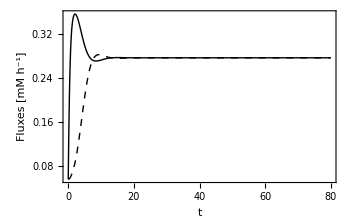

```mathematica
plotSimulation[FilterRules[fluxSol,{v["1"],v["5"]}],FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot,PlotStyle->{Black,Directive[Black,Dashed]},Legend->]
```

```mathematica
Module[{concSol,fluxSol},
Manipulate[
{concSol,fluxSol}=simulate[modelDimer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)},InitialConditions->{m["x8"]->0Millimole Liter^-1}];
GraphicsGrid[{
{plotSimulation[concSol,FrameLabel->{"t","Concentration [mM]"},PlotFunction->Plot],
plotSimulation[fluxSol,FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot]},
{plotSimulation[FilterRules[fluxSol,{v["1"],v["5"]}],FrameLabel->{"t","Fluxes [mM h^-1]"},PlotFunction->Plot,PlotStyle->{Black,Directive[Black,Dashed]}],Show[plotPhasePortrait[FilterRules[fluxSol,{v["1"],v["5"]}],ColorFunction->None,PlotRange->{{0,1.2},{0,1.2}},Mesh->{{.1,1,10,100}},MeshStyle->Directive[PointSize[.03],Red]],Graphics[{Dashed,Line[{{-1,-1},{2.5,2.5}}]}]]}
},ImageSize->600],{{k0,10,Subscript[k, b1]^⟶},0.5,100.},{{tfinal,40},.1,1000}
]
]
AutoCollapse[]
```

Build tetrameric version of

Add the all additional binding reactiosn and adjust the corresponding rate equations for the effective concentrations of the multiple binding sites.

```mathematica
modelTetramer=addReactions[model,additionalBindingReactions];
updateCustomRateLaws[modelTetramer,{"6"->4 Subscript[k, 6]^⟶ x5[t] x6[t]-Subscript[k, 6]^⟵ x7[t],"9"->3 Subscript[k, 6]^⟶ x5[t] x7[t]-2 Subscript[k, 6]^⟵ x8[t],"10"->2 Subscript[k, 6]^⟶ x5[t] x7[t]-3 Subscript[k, 6]^⟵ x9[t],"11"->Subscript[k, 6]^⟶ x5[t] x7[t]-4 Subscript[k, 6]^⟵ x10[t]}]
```

Visualize the relevant binding reactions

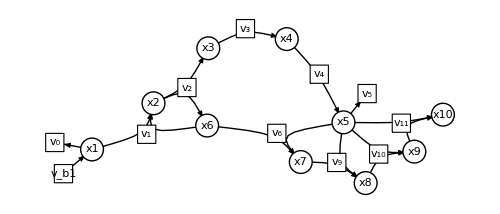

```mathematica
Show[showNetwork[modelTetramer]/.(v[getID[#]]->Style[v[getID[#]],Background->Green,Larger]&/@additionalBindingReactions),ImageSize->500]
```

Initialize the new species at 0 and observe how the relaxes to a new steady state

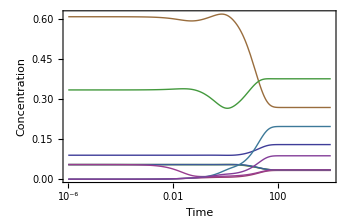

```mathematica
{concSolTetramer,fluxSolTetramer}=simulate[modelTetramer,{t,0,10000},InitialConditions->{m["x8"]->0Millimole Liter^-1,m["x9"]->0Millimole Liter^-1,m["x10"]->0Millimole Liter^-1}];
plotSimulation[concSolTetramer,PlotFunction->LogLinearPlot,FrameLabel->{"Time","Concentration"}]
```

The steady-state equations that have to be solved are

```mathematica
TableForm[ssEq=modelTetramer["ODE"]/.Derivative[1][_metabolite][t]:>0/.elem_[t]:>elem]
```

0==-x1 k_0^⟶-x1 x6 k_1^⟶+x1^Xt k_b1^⟶
0==x1 x6 k_1^⟶-x2 k_2^⟶
0==x2 k_2^⟶-x3 k_3^⟶
0==x3 k_3^⟶-x4 k_4^⟶
0==x4 k_4^⟶-x5 k_5^⟶+4 x10 k_6^⟵+x7 k_6^⟵+2 x8 k_6^⟵+3 x9 k_6^⟵-4 x5 x6 k_6^⟶-6 x5 x7 k_6^⟶
0==-x1 x6 k_1^⟶+x2 k_2^⟶+x7 k_6^⟵-4 x5 x6 k_6^⟶
0==-x7 k_6^⟵+2 x8 k_6^⟵+4 x5 x6 k_6^⟶-3 x5 x7 k_6^⟶
0==-2 x8 k_6^⟵+3 x9 k_6^⟵+x5 x7 k_6^⟶
0==4 x10 k_6^⟵-3 x9 k_6^⟵+x5 x7 k_6^⟶
0==-4 x10 k_6^⟵+x5 x7 k_6^⟶

Left nullspace

```mathematica
Dimensions[modelTetramer][[1]]-MatrixRank[modelTetramer]
NullSpace[modelTetramerᵀ]
conservationRelations=MapIndexed[C[First@#2]==#&,NullSpace[modelTetramerᵀ].modelTetramer["Species"]]
```

1

{{0,1,0,0,0,1,1,1,1,1}}

{C[1]==x10+x2+x6+x7+x8+x9}

Solving the steady-state equations and conservation relation for the species variables yields one real and two complex solutions

```mathematica
ssSol=Solve[Join[ssEq,conservationRelations],modelTetramer["Species"]];
Length[ssSol]
```

3

```mathematica
newIC=(ssSol/.C[1]->1/.Dispatch[stripUnits[modelTetramer["Parameters"]]])[[1]]
```

{x1→0.129999,x2→0.0350004,x3→0.0350004,x4→0.0350004,x5→0.0350004,x6→0.269236,x7→0.376935,x8→0.197893,x9→0.0879527,x10→0.0329822}

```mathematica
updateInitialConditions[modelTetramer,#[[1]]->#[[2]]Millimole Liter^-1&/@newIC]
```

Compare the performance of the core, dimer, and, tetramer system to reject the disturbance in the input flux

```mathematica
Module[{concSol,fluxSol,concSolDimer,fluxSolDimer,concSolTetramer,fluxSolTetramer},
Manipulate[
{concSol,fluxSol}=simulate[model,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0(.1/Hour)}];
{concSolDimer,fluxSolDimer}=simulate[modelDimer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
{concSolTetramer,fluxSolTetramer}=simulate[modelTetramer,{t,0,tfinal},Parameters->{Subscript[k, b1]^⟶ -> k0*(0.1/Hour)}];
Show[plotPhasePortrait[FilterRules[#,{v["1"],v["5"]}]&/@{fluxSol,fluxSolDimer,fluxSolTetramer},ColorFunction->None,PlotRange->{{0,1.2},{0,1.2}},Mesh->{{.1,1,10,100}},MeshStyle->Directive[PointSize[.03],Red],PlotStyle->Thick],Graphics[{Dashed,Line[{{-1,-1},{2.5,2.5}}]}],FrameLabel->{v["1"],v["5"]}],{{k0,10,Subscript[k, b1]^⟶},0.5,100.},{{tfinal,40},.1,1000}
]
]
```

Toolbox::badargs: There is no definition for 'simulate' applicable to modelTetramer, {t, 0, 40}, Parameters → {InterpretationBox[k_StyleBox[.